```mathematica
PacletInstall["https://rulebasedintegration.org/Rubi-4.16.1.0.paclet"]
```

PacletObject[…]

```mathematica
First[PacletFind["Rubi"]]["Location"]
```

C:\Users\Asus\AppData\Roaming\Wolfram\Paclets\Repository\Rubi-4.16.1.0

```mathematica
<<Rubi`
```

```mathematica
f[x_]:=Sqrt[A/(D*x^2+F*x^2+g)]
f[x]
```

√(A/(g+D x^2+F x^2))

```mathematica
√(c/((g+D x^2+F x^2)^2))
```

√(c/((g+D x^2+F x^2)^2))

```mathematica
Steps[Int[f[x],x]]
```

√(A/(g+D x^2+F x^2)) √(g+D x^2+F x^2) Int[1/(√(g+D x^2+F x^2)),x]

√(A/(g+D x^2+F x^2)) √(g+D x^2+F x^2) Int[1/(√(g+(D+F) x^2)),x]

√(A/(g+D x^2+F x^2)) √(g+D x^2+F x^2) Subst[Int[1/(1-(D+F) x^2),x],x,x/(√(g+(D+F) x^2))]

(√(A/(g+D x^2+F x^2)) √(g+D x^2+F x^2) ArcTanh[(√(D+F) x)/(√(g+(D+F) x^2))])/(√(D+F))
Copy Steps

(√(A/(g+D x^2+F x^2)) √(g+D x^2+F x^2) ArcTanh[(√(D+F) x)/(√(g+(D+F) x^2))])/(√(D+F))

```mathematica
g[x_]:=Sqrt[1 - (B^2-4*A*C)/(H*(A*x^2 + B*x+C))]
g[x]
```

√(1-(B^2-4 A C)/(H (C+B x+A x^2)))

```mathematica
Steps[Int[g[x],x]]
Integrate[g[x],x]
```

Int[√(1-(B^2-4 A C)/(H (C+B x+A x^2))),x]
Copy Steps

```mathematica
Integrate[√(1-F/(C+B x+A x^2)),x]//Simplify
```

(√((A (C+x (B+A x)))/(-B^2+4 A C)) √((C-F+x (B+A x))/(C+x (B+A x))) EllipticE[ArcSin[(√(A^2/(B^2-4 A C)) (B+2 A x))/A],(B^2-4 A C)/(B^2-4 A C+4 A F)])/(2 √(A^2/(B^2-4 A C)) √(-(A (C-F+x (B+A x)))/(B^2+4 A (-C+F))))

```mathematica
f[x_]:=((15*β)/(α*ϕ^2+β*x^2+γ*ϕ*x))[1-(ϕ^2/(48*β*((ν-12α)*ϕ^2+(ϵ-12β)*x^2+(σ-12γ)*ϕ*x)))[(σ-12γ)^2 - 4*(ϵ-12β)*(ν-12α)]] -3/2*(2*β*x+γ*ϕ)^2/((α*ϕ^2+β*x^2+γ*ϕ*x)^2)
f[x]
```

-(3 (2 x β+γ ϕ)^2)/(2 (x^2 β+x γ ϕ+α ϕ^2)^2)+(15 β)/(x^2 β+x γ ϕ+α ϕ^2)[1-ϕ^2/(48 β (x^2 (-12 β+ϵ)+x (-12 γ+σ) ϕ+(-12 α+ν) ϕ^2))[-4 (-12 β+ϵ) (-12 α+ν)+(-12 γ+σ)^2]]

```mathematica
g[x_]:=Sqrt[((15*β)/(α*ϕ^2+β*x^2+γ*ϕ*x))[-(ϕ^2/(48*β*((ν-12α)*ϕ^2+(ϵ-12β)*x^2+(σ-12γ)*ϕ*x)))[(σ-12γ)^2 - 4*(ϵ-12β)*(ν-12α)]] -3/2*(2*β*x+γ*ϕ)^2/((α*ϕ^2+β*x^2+γ*ϕ*x)^2)]//Simplify
g[x]//Simplify
```

√(-(3 (2 x β+γ ϕ)^2)/(2 (x^2 β+x γ ϕ+α ϕ^2)^2)+(15 β)/(x^2 β+x γ ϕ+α ϕ^2)[-ϕ^2/(48 β (x^2 (-12 β+ϵ)+x (-12 γ+σ) ϕ+(-12 α+ν) ϕ^2))[-4 (-12 β+ϵ) (-12 α+ν)+(-12 γ+σ)^2]])

```mathematica
Steps[Int[g[x],x]]
```

Int[√(-(3 (2 x β+γ ϕ)^2)/(2 (x^2 β+x γ ϕ+α ϕ^2)^2)+(15 β)/(x^2 β+x γ ϕ+α ϕ^2)[-ϕ^2/(48 β (x^2 (-12 β+ϵ)+x (-12 γ+σ) ϕ+(-12 α+ν) ϕ^2))[-4 (-12 β+ϵ) (-12 α+ν)+(-12 γ+σ)^2]]),x]
Copy Steps

Int[√(-(3 (2 x β+γ ϕ)^2)/(2 (x^2 β+x γ ϕ+α ϕ^2)^2)+(15 β)/(x^2 β+x γ ϕ+α ϕ^2)[-ϕ^2/(48 β (x^2 (-12 β+ϵ)+x (-12 γ+σ) ϕ+(-12 α+ν) ϕ^2))[-4 (-12 β+ϵ) (-12 α+ν)+(-12 γ+σ)^2]]),x]

```mathematica
h[x_]:=Integrate[Sqrt[f[x]],x]
h[x]
```

∫√(-(3 (2 x β+γ ϕ)^2)/(2 (x^2 β+x γ ϕ+α ϕ^2)^2)+(15 β)/(x^2 β+x γ ϕ+α ϕ^2)[1-ϕ^2/(48 β (x^2 (-12 β+ϵ)+x (-12 γ+σ) ϕ+(-12 α+ν) ϕ^2))[-4 (-12 β+ϵ) (-12 α+ν)+(-12 γ+σ)^2]])ⅆx

```mathematica
InverseFunction[h]
```

h^(-1)

```mathematica
j[x_]:=((15*β*(β*x^2+(β+γ*ϕ)*x+(α+γ/2)*ϕ^2)^2)/(α*ϕ^2+β*x^2+γ*ϕ*x))[1-(ϕ^2/(48*β*((ν-12α)*ϕ^2+(ϵ-12β)*x^2+(σ-12γ)*ϕ*x)))[(σ-12γ)^2 - 4*(ϵ-12β)*(ν-12α)]] -3/2*(2*β*x+γ*ϕ)^2/((α*ϕ^2+β*x^2+γ*ϕ*x)^2)
j[x]
```

-(3 (2 x β+γ ϕ)^2)/(2 (x^2 β+x γ ϕ+α ϕ^2)^2)+(15 β (x^2 β+(α+γ/2) ϕ^2+x (β+γ ϕ))^2)/(x^2 β+x γ ϕ+α ϕ^2)[1-ϕ^2/(48 β (x^2 (-12 β+ϵ)+x (-12 γ+σ) ϕ+(-12 α+ν) ϕ^2))[-4 (-12 β+ϵ) (-12 α+ν)+(-12 γ+σ)^2]]

```mathematica
Steps[Int[j[x],x]]
```

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

Removed[Int][(15 β (x^2 β+(α+γ/2) ϕ^2+x (β+γ ϕ))^2)/(x^2 β+x γ ϕ+α ϕ^2)[TerminatedEvaluation[IterationLimit]],x]-Dist[3/2,Removed[Int][(2 x β+γ ϕ)^2/((x^2 β+x γ ϕ+α ϕ^2)^2),x],x]
Copy Steps

Removed[Int][(15 β (x^2 β+(α+γ/2) ϕ^2+x (β+γ ϕ))^2)/(x^2 β+x γ ϕ+α ϕ^2)[TerminatedEvaluation[IterationLimit]],x]-Dist[3/2,Removed[Int][(2 x β+γ ϕ)^2/((x^2 β+x γ ϕ+α ϕ^2)^2),x],x]

```mathematica
Integrate[j[x],x]
```

-(3 (-2 x β-γ ϕ))/(2 (x^2 β+x γ ϕ+α ϕ^2))+(6 β ArcTanh[(2 x β+γ ϕ)/(√(-4 α β+γ^2) ϕ)])/(√(-4 α β+γ^2) ϕ)+x (15 β (x^2 β+(α+γ/2) ϕ^2+x (β+γ ϕ))^2)/(x^2 β+x γ ϕ+α ϕ^2)[1-ϕ^2/(48 β (x^2 (-12 β+ϵ)+x (-12 γ+σ) ϕ+(-12 α+ν) ϕ^2))[-4 (-12 β+ϵ) (-12 α+ν)+(-12 γ+σ)^2]]

```mathematica
Integrate[Sqrt[j[x]],x]
```

∫√(-(3 (2 x β+γ ϕ)^2)/(2 (x^2 β+x γ ϕ+α ϕ^2)^2)+(15 β (x^2 β+(α+γ/2) ϕ^2+x (β+γ ϕ))^2)/(x^2 β+x γ ϕ+α ϕ^2)[1-ϕ^2/(48 β (x^2 (-12 β+ϵ)+x (-12 γ+σ) ϕ+(-12 α+ν) ϕ^2))[-4 (-12 β+ϵ) (-12 α+ν)+(-12 γ+σ)^2]])ⅆx

```mathematica
g[x_]:=((ν-12α)*ϕ^2+(ϵ-12β)*x^2+(σ-12γ)*ϕ*x)

g[x]
```

x^2 (-12 β+ϵ)+x (-12 γ+σ) ϕ+(-12 α+ν) ϕ^2

```mathematica
Integrate[f[x],x]
```

```mathematica
f[x_]:=(1+1/g[x])^-(1)
f[x]
h[x_]:= 1+ A/(2*g[x])
h[x]
i[x_,A_]:= Sqrt[1- A/g[x]]
i[x,A]
```

1/(1+1/(x^2 (-12 β+ϵ)+x (-12 γ+σ) ϕ+(-12 α+ν) ϕ^2))

1+A/(2 (x^2 (-12 β+ϵ)+x (-12 γ+σ) ϕ+(-12 α+ν) ϕ^2))

√(1-A/(x^2 (-12 β+ϵ)+x (-12 γ+σ) ϕ+(-12 α+ν) ϕ^2))

```mathematica
j[x_]:=Integrate[h[x],x]
j[x]
```

x-(A ArcTanh[(24 x β-2 x ϵ+12 γ ϕ-σ ϕ)/(√(-576 α β+144 γ^2+48 α ϵ+48 β ν-4 ϵ ν-24 γ σ+σ^2) ϕ)])/(√(-576 α β+144 γ^2+48 α ϵ+48 β ν-4 ϵ ν-24 γ σ+σ^2) ϕ)

```mathematica
l[x_]:=Integrate[h[x],x]
l[x]
```

x+(A ArcTanh[(24 x β-2 x ϵ+12 γ ϕ-σ ϕ)/(√(-576 α β+144 γ^2+48 α ϵ+48 β ν-4 ϵ ν-24 γ σ+σ^2) ϕ)])/(√(-576 α β+144 γ^2+48 α ϵ+48 β ν-4 ϵ ν-24 γ σ+σ^2) ϕ)

```mathematica
(-4*(ν-12α)*(ϵ-12β)+(σ-12γ)^2)//Expand
```

-576 α β+144 γ^2+48 α ϵ+48 β ν-4 ϵ ν-24 γ σ+σ^2

```mathematica
Series[i[x,A],{A,0,2}]
m[x_]:=Series[l[x],{x,0,2}]
m[x]
```

1-A/(2 (x^2 (-12 β+ϵ)+x (-12 γ+σ) ϕ+(-12 α+ν) ϕ^2))-A^2/(8 (x^2 (-12 β+ϵ)+x (-12 γ+σ) ϕ+(-12 α+ν) ϕ^2)^2)+O[A]^3

(A ArcTanh[(12 γ-σ)/(√(-576 α β+144 γ^2+48 α ϵ+48 β ν-4 ϵ ν-24 γ σ+σ^2))])/(√(-576 α β+144 γ^2+48 α ϵ+48 β ν-4 ϵ ν-24 γ σ+σ^2) ϕ)+(1-A/(2 (12 α-ν) ϕ^2)) x+(A (12 γ-σ) x^2)/(4 (12 α-ν)^2 ϕ^3)+O[x]^3

```mathematica
m[x_]:=(A ArcTanh[(12 γ-σ)/(√(-576 α β+144 γ^2+48 α ϵ+48 β ν-4 ϵ ν-24 γ σ+σ^2))])/(√(-576 α β+144 γ^2+48 α ϵ+48 β ν-4 ϵ ν-24 γ σ+σ^2) ϕ)+(1-A/(2 (12 α-ν) ϕ^2)) x+(A (12 γ-σ) x^2)/(4 (12 α-ν)^2 ϕ^3)
Solve[m[x]==y,x]
```

{{x→(2 (12 α-ν)^2 ϕ^3 (-1+A/(2 (12 α-ν) ϕ^2)-√((1-A/(2 (12 α-ν) ϕ^2))^2-(A (12 γ-σ) (-y+(A ArcTanh[(12 γ-σ)/(√(-576 α β+144 γ^2+48 α ϵ+48 β ν-4 ϵ ν-24 γ σ+σ^2))])/(√(-576 α β+144 γ^2+48 α ϵ+48 β ν-4 ϵ ν-24 γ σ+σ^2) ϕ)))/((12 α-ν)^2 ϕ^3))))/(A (12 γ-σ))},{x→(2 (12 α-ν)^2 ϕ^3 (-1+A/(2 (12 α-ν) ϕ^2)+√((1-A/(2 (12 α-ν) ϕ^2))^2-(A (12 γ-σ) (-y+(A ArcTanh[(12 γ-σ)/(√(-576 α β+144 γ^2+48 α ϵ+48 β ν-4 ϵ ν-24 γ σ+σ^2))])/(√(-576 α β+144 γ^2+48 α ϵ+48 β ν-4 ϵ ν-24 γ σ+σ^2) ϕ)))/((12 α-ν)^2 ϕ^3))))/(A (12 γ-σ))}}

```mathematica
k[x_]:= (Sqrt[5]*A)/(4*Sqrt[g[x]])+(6*Sqrt[5]*B*Sqrt[g[x]])/A
k[x]
```

(√5 A)/(4 √(x^2 (-12 β+ϵ)+x (-12 γ+σ) ϕ+(-12 α+ν) ϕ^2))+(6 √5 B √(x^2 (-12 β+ϵ)+x (-12 γ+σ) ϕ+(-12 α+ν) ϕ^2))/A

```mathematica
c = 1000
r = 1
A = 1
```

1000

1

1

```mathematica
v[x_]:= Tanh[A - Tanh[(x+r)/c]]
v[x]
```

Tanh[1-Tanh[(1+x)/1000]]

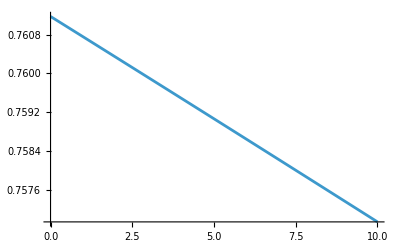

```mathematica
Plot[v[x],{x,0,10}]
```